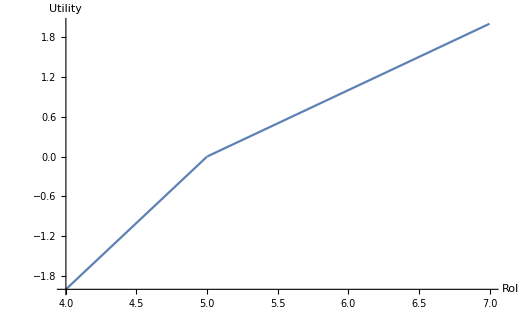

```mathematica
Plot[Max[x-5,0]-2Max[5-x,0],{x,4,7},AxesLabel->{"RoI","Utility"},AxesOrigin->{4,-2},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14}]
```

```mathematica
stocks={"MSFT","AAPL","GOOG"};
y=2015;
```

```mathematica
solveObjective[{"MSFT"},2015];
```

LinearProgramming::lpsub: This problem is unbounded.

```mathematica
xs=adjustFeaturesMatrix[x[y]/@stocks];
rs=Flatten[r[y]/@stocks,1];
```

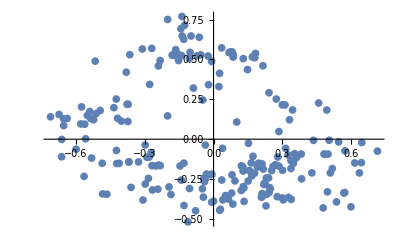

```mathematica
ListPlot@
Flatten[
Map[Function[xStock,
(*#[[3;;4]]&/@xStock]*)
Transpose@MapThread[Standardize[{##},Mean,Function[3StandardDeviation[##]]]&,#[[3;;4]]&/@xStock]],
xs],
1]
```

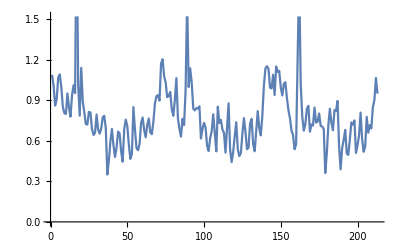

```mathematica
ListLinePlot[Norm/@Flatten[
Map[Function[xStock,
Transpose@MapThread[Standardize[{##},Mean,Function[3StandardDeviation[##]]]&,xStock]],
xs],
1]]
```

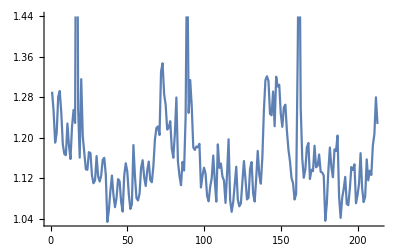

```mathematica
ListLinePlot[Norm/@adjustFeaturesMatrix@xs]
```

```mathematica
n=8;p=3;
```

```mathematica
μs=rangeVars[μ,n];
λs=rangeVars[λ,n];
qs=rangeVars[q,p];
```

```mathematica
μs.ones[n]-2λs.ones[n]
```

-2 (λ$1+λ$2+λ$3+λ$4+λ$5+λ$6+λ$7+λ$8)+μ$1+μ$2+μ$3+μ$4+μ$5+μ$6+μ$7+μ$8

```mathematica
ones
```

ones

```mathematica
2ones[n]
```

{2,2,2,2,2,2,2,2}

```mathematica
-2λs.ones[n]
```

-2 λ$1

```mathematica
{x,y}≤{0,1}
```

{x,2015}≤{0,1}

```mathematica
LessEqual[x,3]
```

x≤3

```mathematica
GreaterEqual
```

```mathematica
μs
```

{μ$1,μ$2,μ$3,μ$4,μ$5,μ$6,μ$7,μ$8}

```mathematica
Thread[GreaterEqual[μs~Join~λs,0]]
```

{μ$1≥0,μ$2≥0,μ$3≥0,μ$4≥0,μ$5≥0,μ$6≥0,μ$7≥0,μ$8≥0,λ$1≥0,λ$2≥0,λ$3≥0,λ$4≥0,λ$5≥0,λ$6≥0,λ$7≥0,λ$8≥0}

```mathematica
μs~Join~λs~Join~qs
```

{μ$1,μ$2,μ$3,μ$4,μ$5,μ$6,μ$7,μ$8,λ$1,λ$2,λ$3,λ$4,λ$5,λ$6,λ$7,λ$8,q$1,q$2,q$3}

```mathematica
Norm[qs]
```

√(Abs[q$1]^2+Abs[q$2]^2+Abs[q$3]^2)

```mathematica
Thread[GreaterEqual[μs~Join~λs,0]]
~Join~
{Norm[qs]≤1}
```

{μ$1≥0,μ$2≥0,μ$3≥0,μ$4≥0,μ$5≥0,μ$6≥0,μ$7≥0,μ$8≥0,λ$1≥0,λ$2≥0,λ$3≥0,λ$4≥0,λ$5≥0,λ$6≥0,λ$7≥0,λ$8≥0,√(Abs[q$1]^2+Abs[q$2]^2+Abs[q$3]^2)≤1}

```mathematica
rs
```

rs

```mathematica
ans=solveObjective[{"MSFT"},2015]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 200 iterations.

{9.33321,{μ$1→3.07129,μ$2→1.68777,μ$3→1.83291,μ$4→5.19754,μ$5→1.21158,λ$1→0.791157,λ$2→0.266747,λ$3→0.12937,λ$4→0.,λ$5→0.646659,q$1→0.701354,q$2→-0.00370146,q$3→-0.153053,q$4→0.0201385,q$5→-0.060979,q$6→-0.557798,q$7→-0.272227}}

```mathematica
{Norm[qs/.ans[[2]]]}
```

{0.904256}

```mathematica
xs//TableForm
```

1 | 0.471641 | -0.594208 | 0.578483 | -0.0706598 | -0.476659 | -0.166945
1 | -0.484927 | -0.518082 | 0.504432 | -0.0913094 | -0.485962 | 0.0308606
1 | -0.245785 | -0.518082 | 0.387326 | -0.0906089 | -0.49192 | -0.0234015
1 | -0.00664283 | -0.518082 | 0.487209 | -0.0910397 | -0.520253 | -0.146758
1 | 0.232499 | -0.518082 | 0.721421 | -0.0727367 | -0.509377 | -0.137824

```mathematica
SystemOpen@FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

```mathematica
Needs["MATLink`"]
```

n$::shdw: Symbol "n$" appears in multiple contexts {"MATLink`Private`", "Global`"}; definitions in context "MATLink`Private`" may shadow or be shadowed by other definitions.

```mathematica
OpenMATLAB[]
```

```mathematica
MEvaluate["mat = magic(4)"]
```

>> 
mat =

    16     2     3    13
     5    11    10     8
     9     7     6    12
     4    14    15     1

```mathematica
mat=MGet["mat"];
```

```mathematica
mat
```

{{16.,2.,3.,13.},{5.,11.,10.,8.},{9.,7.,6.,12.},{4.,14.,15.,1.}}

```mathematica
v={1,2,3};
```

```mathematica
MSet["v",v]
```

```mathematica
MGet["v"]
```

{1.,2.,3.}

```mathematica
MSet["xs",xs]
```

```mathematica
MSet["rs",rs]
```

```mathematica
MEvaluate["xs"]
```

```mathematica
xs
```

{{1,0.471641,-0.594208,0.578483,-0.0706598,-0.476659,-0.166945},{1,-0.484927,-0.518082,0.504432,-0.0913094,-0.485962,0.0308606},{1,-0.245785,-0.518082,0.387326,-0.0906089,-0.49192,-0.0234015},{1,-0.00664283,-0.518082,0.487209,-0.0910397,-0.520253,-0.146758},{1,0.232499,-0.518082,0.721421,-0.0727367,-0.509377,-0.137824}}

```mathematica
"["<>StringReplace[ToString[xs],{"},"->";","{"->"","}"->""}]<>"]"
```

[1, 0.471641, -0.594208, 0.578483, -0.0706598, -0.476659, -0.166945; 1, -0.484927, -0.518082, 0.504432, -0.0913094, -0.485962, 0.0308606; 1, -0.245785, -0.518082, 0.387326, -0.0906089, -0.49192, -0.0234015; 1, -0.00664283, -0.518082, 0.487209, -0.0910397, -0.520253, -0.146758; 1, 0.232499, -0.518082, 0.721421, -0.0727367, -0.509377, -0.137824]

```mathematica
toMatlabMatrix[xs]
```

[1, 0.471641, -0.594208, 0.578483, -0.0706598, -0.476659, -0.166945; 1, -0.484927, -0.518082, 0.504432, -0.0913094, -0.485962, 0.0308606; 1, -0.245785, -0.518082, 0.387326, -0.0906089, -0.49192, -0.0234015; 1, -0.00664283, -0.518082, 0.487209, -0.0910397, -0.520253, -0.146758; 1, 0.232499, -0.518082, 0.721421, -0.0727367, -0.509377, -0.137824]

```mathematica
toMatlabMatrix[rs]
```

[-0.00919586, -0.0146774, 0.0127053, 0.0294184, -0.00840526]

```mathematica
n
```

5

```mathematica
rs//toMatlabMatrix
```

[-0.00919586, -0.0146774, 0.0127053, 0.0294184, -0.00840526, -0.0125026, -0.00515013, -0.00862827, -0.0104439, 0.0167107, 0.00324394, -0.0101315, 0.0263504, 0.00106075, -0.00360325, -0.0925335, -0.0344585, 0.0199076, -0.0383241, 0.0217821, 0.00775197, 0.00576937, 0.0145794, -0.000942348, -0.00117905, 0.00566563, -0.00516419, 0.0167531, 0.0181017, 0.00757576, -0.00114732, -0.00068918, 0.00827586, 0.00661195, -0.001359, -0.00226809, 0.00159127, -0.00476623, 0.000684151, -0.0136737, -0.00508318, 0.00116117, -0.0173974, 0.0115675, -0.0191365, -0.00118963, -0.022868, 0.00877621, 0.00434993, 0.00336862, 0.0191847, -0.00494118, 0.0139513, -0.000466418, 0.000933271, -0.0335664, -0.00602991, -0.00582383, -0.000244081, -0.00732422, 0.00147565, -0.0105599, 0.0312733, -0.000481348, -0.00264869, 0.00144858, 0.00578592, 0.000958773, -0.0026341, 0.0146459, -0.0023663, -0.0128083]